Jai Prasadh
HW 8

```mathematica
Clear[H, L, x, n, nmax, A, B, B0, B00, a, b]
```

```mathematica
(* Problem 1a *)
```

```mathematica
B00 = (1/(2 L)) Integrate[1,{x,0,L/2}];
a= (1/L) Integrate[Sin[(2 Pi n x)/(2L)], {x,0,L/2}];
b=(1/L) Integrate[Cos[(2 Pi n x)/(2L)], {x,0,L/2}];
B0=1/4;
A[n_]:=(2 Sin[(n π)/4]^2)/(n π);
B[n_]:=Sin[(n π)/2]/(n π);
```

```mathematica
nmax =3;
f[x_]:=B0+Sum[A[n] Sin[(2n Pi x)/(2L)]+B[n] Cos[(2n Pi x)/(2L)] ,{n,nmax}];
Normal[f[x]]
```

1/4+Cos[(π x)/L]/π-Cos[(3 π x)/L]/(3 π)+Sin[(π x)/L]/π+Sin[(2 π x)/L]/π+Sin[(3 π x)/L]/(3 π)

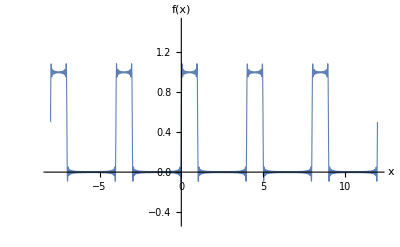

```mathematica
L=2;
nmax=50;

Plot[f[x], {x,-4L,6L},AxesLabel->{"x","f(x)"},PlotStyle->Thickness[0.002],PlotRange->{-0.5,1.5}]
```

```mathematica
(* Problem 1b *)
Clear[H, L, x, n, nmax, A, B, B0, B00, a, b]
```

```mathematica
B00 = (1/(2 L)) Integrate[x^2,{x,-L,L}];
a= (1/L) Integrate[(x^2)Sin[(2 Pi n x)/(2L)], {x,-L,L}];
b=(1/L) Integrate[(x^2)Cos[(2 Pi n x)/(2L)], {x,-L,L}];
B0=4/3;
A[n_]:=0;
B[n_]:=(8 (2 n π Cos[n π]+(-2+n^2 π^2) Sin[n π]))/(n^3 π^3);
```

```mathematica
nmax =3;
f[x_]:=B0+Sum[A[n] Sin[(2n Pi x)/(2L)]+B[n] Cos[(2n Pi x)/(2L)] ,{n,nmax}];
Normal[f[x]]
```

4/3-(16 Cos[(π x)/L])/π^2+(4 Cos[(2 π x)/L])/π^2-(16 Cos[(3 π x)/L])/(9 π^2)

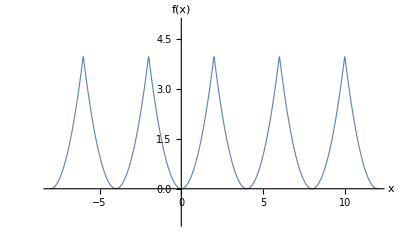

```mathematica
L=2;
nmax=50;

Plot[f[x], {x,-4L,6L},AxesLabel->{"x","f(x)"},PlotStyle->Thickness[0.002],PlotRange->{-1,5}]
```

```mathematica
(* Problem 2a *)
Clear[H, L, x, n, nmax, A, B, B0, B00, a, b, z]
```

```mathematica
Efield[z_]:=Piecewise[{{E0 Cos[k0 z], Abs[z]≤L/2},{0, Abs[z]> L/2}}];
SquigglyEfield[k_]:=FourierTransform[Efield[z],z,k,Assumptions->{L∈Reals, L>0}];
Normal[SquigglyEfield[k]]
```

((-300+k) Sin[1/2 (300+k) L]-(300+k) Sin[150 L-(k L)/2])/((-90000+k^2) √(2 π))

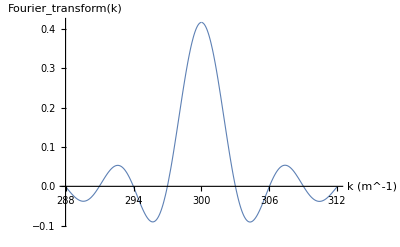

```mathematica
(* b) *)
SquigglyE[k_]:=(E0/Sqrt[2 Pi])((Sin[(k-k0)L/2]/(k-k0))+(Sin[(k+k0)L/2]/(k+k0)))

E0=1;
k0=300;
L=2.09;

Plot[SquigglyE[k], {k,k0-(8 Pi/L),k0+(8 Pi/L)},AxesLabel->{"k (m^-1)","Fourier_transform(k)"},PlotStyle->Thickness[0.002]]
```

```mathematica
(* c) *)
FindRoot[SquigglyE[k],{k,299}]
FindRoot[SquigglyE[k],{k,302}]
```

{k→296.989}

{k→303.011}

```mathematica
dk=303.0109298764481-296.98901171161106
```

6.02192

```mathematica
uncertaintyproduct=6.021918164837018*2.09
```

12.5858

```mathematica
(* d *)
```

```mathematica
Clear[H, L, x, n, nmax, A, B, B0, B00, a, b, z,k, E0, k0]
```

```mathematica
Efield[0,t_]:=Piecewise[{{E0 Cos[ω0 t], Abs[t]≤L/(2v)},{0, Abs[t]> L/(2v)}}];
SquigglyEfield[ω_]:=FourierTransform[Efield[0,t],t,ω,Assumptions->{L∈Reals, L>0,v∈Reals, v>0}];
Normal[SquigglyEfield[ω]]
```

1/(√(2 π) (-396900.+ω^2))(-1260. E0 Cos[(0.238095+0. ⅈ) L ω] Sin[(150.+0. ⅈ) L]+2. E0 ω Cos[(150.+0. ⅈ) L] Sin[(0.238095+0. ⅈ) L ω])

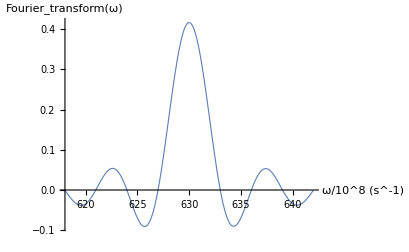

```mathematica
SquigglyE[ω_]:=(E0/Sqrt[2 Pi])((Sin[(ω-ω0)L/2]/(ω-ω0))+(Sin[(ω+ω0)L/2]/(ω+ω0)));

E0=1;
k0=300;
L=2.09;
v=0.7 * (3*10^0); (* took out factor of 10^8 to make graph scale reasonable *)
ω0=v k0;

Plot[SquigglyE[ω], {ω,ω0-12,ω0+12},AxesLabel->{"ω/10^8 (s^-1)","Fourier_transform(ω)"},PlotStyle->Thickness[0.002]]
```

```mathematica
(* e *)
FindRoot[SquigglyE[ω],{ω,ω0-3}]
FindRoot[SquigglyE[ω],{ω,ω0+3}]
```

{ω→626.993}

{ω→633.007}

```mathematica
dω=(633.0071401965845-626.9928595308697)*10^8
dt=L/(v*10^8)
dω dt
```

6.01428×10^8

9.95238×10^-9

5.98564

```mathematica
(* 3.
a, b
*)
ClearAll["Global`*"]
```

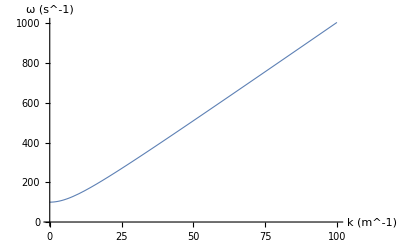

```mathematica
w[k_]:=((a^2)( k^2) + (wc)^2)^0.5;
a=10;
wc=100;
Plot[w[k], {k,0,100},AxesLabel->{"k (m^-1)","ω (s^-1)"},PlotStyle->Thickness[0.002]]
```

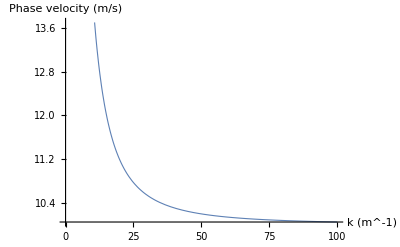

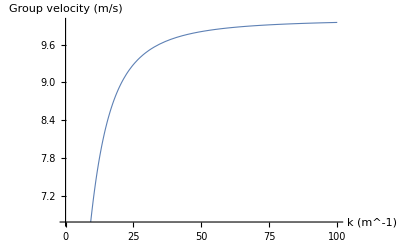

```mathematica
(* c, d *)
(* as functions of k *)
vp[k_]:=((a^2)+ (wc/k)^2)^0.5;
vg[k_]:=((a^2)k)((a^2)( k^2) + (wc)^2)^(-0.5);

Plot[vp[k], {k,0,100},AxesLabel->{"k (m^-1)","Phase velocity (m/s)"},PlotStyle->Thickness[0.002]]
Plot[vg[k], {k,0,100},AxesLabel->{"k (m^-1)","Group velocity (m/s)"},PlotStyle->Thickness[0.002]]
```

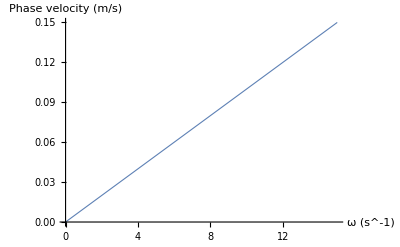

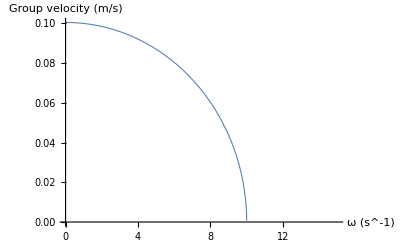

```mathematica
(* as functions of ω*)
vp[w_]:=(w^2 /-((w/a)^2 -(wc)^2))^(0.5);
vg[w_]:=(((a w)^2-(wc)^2)/(w^2 + (1-a^2)wc^2))^0.5;

Plot[vp[w], {w,0,15},AxesLabel->{"ω (s^-1)","Phase velocity (m/s)"},PlotStyle->Thickness[0.002]]
Plot[vg[w], {w,0,15},AxesLabel->{"ω (s^-1)","Group velocity (m/s)"},PlotStyle->Thickness[0.002]]
```

```mathematica
(* 4 c,d *)
kavg=5;
kmod=0.5;
wavg=200;
wmod=30;
ψ0=0.5;
B=2ψ0;
t1=Pi/(2 wmod);

ψ[z_,t_]:=B Cos[wmod t - kmod z]Cos[wavg t-kavg z];
```

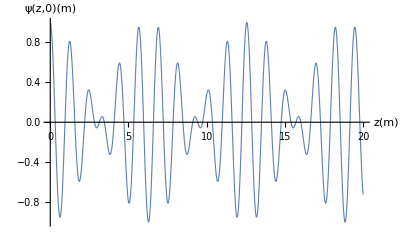

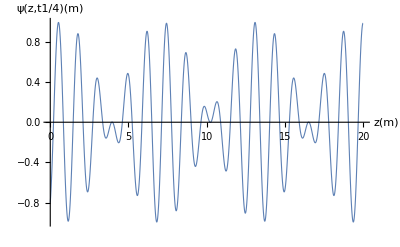

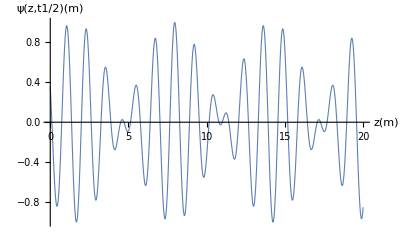

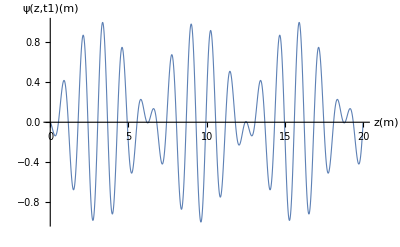

```mathematica
Plot[ψ[z,0], {z,0,20},AxesLabel->{"z(m)","ψ(z,0)(m)"},PlotStyle->Thickness[0.002]]
Plot[ψ[z,t1/4], {z,0,20},AxesLabel->{"z(m)","ψ(z,t1/4)(m)"},PlotStyle->Thickness[0.002]]
Plot[ψ[z,t1/2], {z,0,20},AxesLabel->{"z(m)","ψ(z,t1/2)(m)"},PlotStyle->Thickness[0.002]]
Plot[ψ[z,t1], {z,0,20},AxesLabel->{"z(m)","ψ(z,t1)(m)"},PlotStyle->Thickness[0.002]]
```

```mathematica
vp=wavg/kavg;
vg=wmod/kmod;
peakdistance=vp*t1//N
groupdistance=vg*t1//N
```

2.0944

3.14159

These are the correct distances since it is qualitatively apparent that a particular peak travels slightly more than 2 meters in time t1, and the envelope looks like a cosine at t=0 whereas it looks like a sine at t=t1, so it makes sense that the group travels a distance of pi meters in time t1.